Points:

{{2,10},{7,1},{15,3},{18,10}}

Ftilde definition:

Piecewise[{{10-9/5 (-2+x), x≥2&&x≤7}, {1+1/4 (-7+x), x≥7&&x≤15}, {3+7/3 (-15+x), x≥15&&x≤18}, {0, True}}]

Density function:

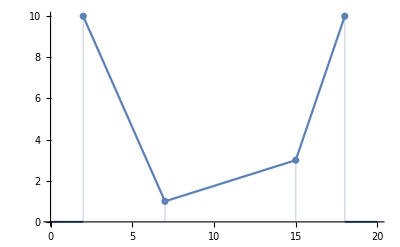

Area:

63

f definition:

Piecewise[{{1/63 (10-9/5 (-2+x)), x≥2&&x≤7}, {1/63 (1+1/4 (-7+x)), x≥7&&x≤15}, {1/63 (3+7/3 (-15+x)), x≥15&&x≤18}, {0, True}}]

Repartition function

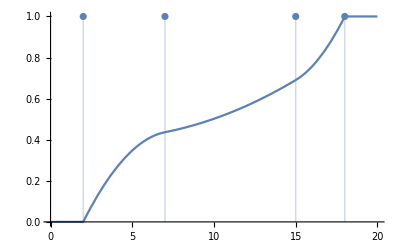

```mathematica
(* Parameters *)
numeric=True;
a=2;
b=18;
n=3;

(* Generate points *)
If[numeric,
seed=Take[
DeleteDuplicates[
(* Generate enough value to defeat duplicates *)
RandomInteger[{a+1, b-1}, n ^2]
],n-1];
xs=Sort[Join[{a},seed,{b}]];
ys=RandomInteger[{1,10}]&/@xs;
,
xs=Table[Subscript[x, k],{k,1,n+1}];
ys= Table[Subscript[y, k],{k,1,n+1}];
]

Print["Points:"];
point:={xs[[#]], ys[[#]]}&
ps= Table[point[i],{i,1,n+1}]

(* Build ftilde pieces *)
parts=Table[
Block[{
x0=xs[[i]],
x1=xs[[i+1]],
y0=ys[[i]],
y1=ys[[i+1]]
},Block[{m=(y1-y0)/(x1-x0)}, {m*(x-x0)+y0,x≥x0&&x≤x1}]]
,{i,1,n}];

Print["Ftilde definition:"];
ftilde=Piecewise[parts, 0]

(* Display ftilde graph *)
If[numeric,
Print["Density function:"];
Show[
Plot[ftilde,{x,0,20}],
ListPlot[ps,Filling->Axis]
]
]

(* Compute area *)
Print["Area:"];
If[numeric,
area=Integrate[ftilde,{x,-Infinity,Infinity}]
,
partsarea=Table[
Block[{
x0=xs[[i]],
x1=xs[[i+1]],
y0=ys[[i]],
y1=ys[[i+1]]
},((y0+y1)(x1-x0))/2]
,{i,1,n}];
area=Fold[#1+#2&,partsarea]
]

(* Define f *)
Print["f definition:"];
fparts=Map[{#[[1]]/area,#[[2]]}&,parts];
f=Piecewise[fparts,0]

(* Repartition function *)
If[numeric,
Print["Repartition function"];
Show[
Plot[Integrate[f,{x,0,i}],{i,0,20}],
ListPlot[Map[{#,1}&,xs],Filling->Axis]
]
]
```